## Log branch point analysis

```mathematica
LogB[x_,bp_]:=Module[{l=Log[x]},If[Im[l]≥bp,l,l+2π I]];
```

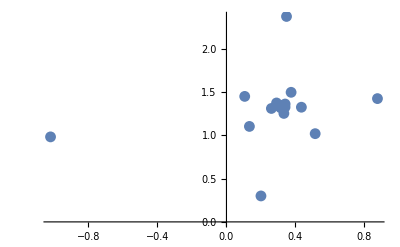

```mathematica
bp=-π;
ListPlot[Table[RepFunc[LogB[#,bp]&,n][0.2+0.3I],{n,0,30}]//CPnts,PlotRange->Full]
```

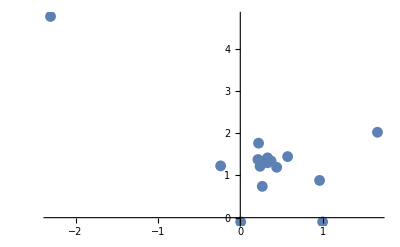

```mathematica
bp=-0.2;
ListPlot[Table[RepFunc[LogB[#,bp]&,n][1-0.1I],{n,0,30}]//CPnts,PlotRange->Full]
```

```mathematica
Im[CP]-π
```

-1.80436

```mathematica
Im[CP]+π
```

4.47883